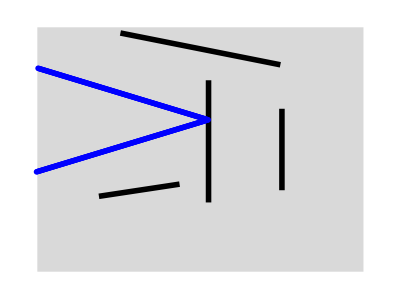

```mathematica
OpticSimulate[{4,3}, {{0.1,0.1,0,1.5,BasicMirror[]}, {1,0,0,1,BasicMirror[]}, {-0.75, -0.5, Pi/2-0.15, 1, BasicMirror[]}, {0,1.235,9Pi/16,2,BasicMirror[]}}]
```

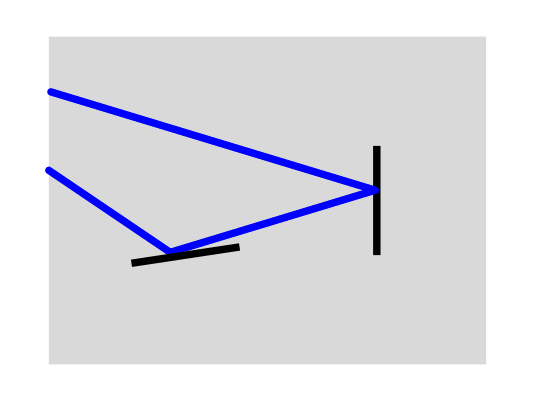

```mathematica
OpticSimulate[dims_, elements_List, OptionsPattern[{ExecLimit->10000, Sources->{{-2,1,-3Pi/32, 0.02}}, Size->0.05}]]:=Module[{canvas, source, res, graphics, velX, velY},
canvas = Rectangle[{-(dims[[1]])/2, -(dims[[2]])/2}, {(dims[[1]])/2, (dims[[2]])/2}];

source = OptionValue[Sources][[1]];
velX = source[[4]] Cos[source[[3]]];
velY = source[[4]]Sin[source[[3]]];
source[[3]]=velX;
source[[4]]=velY;

res = SimulBeam[dims, elements, source, OptionValue[ExecLimit]];

graphics = {LightGray, canvas, Blue, PointSize[0.01], Point[res]};
Do[
AppendTo[graphics, #] & /@ elem[[5]]["graphics"][elem[[1]],elem[[2]],elem[[3]],elem[[4]]];
,{elem, elements}];

Return[Graphics[graphics]];
]
OpticSimulate[{4,3}, {{1,0,0,1,BasicMirror[]}, {-0.75, -0.5, Pi/2-0.15, 1, BasicMirror[]}}]
```

```mathematica
BasicMirror[]:=Module[{check, update,  render},
check[x_, y_, xV_, yV_] := Sign[x]!=Sign[x + xV];
update[x_, y_, xV_, yV_] := Module[{res},
res = ToPolarCoordinates[{yV, xV}];
res[[1]]=res[[1]];
res[[2]]=2Pi-res[[2]];
If[res[[2]]>Pi,res[[2]]=res[[2]]-2Pi];
If[res[[2]]<=-Pi,res[[2]]=res[[2]]+2Pi];
res = FromPolarCoordinates[res];
Return[{x, y, res[[2]], res[[1]]}]
];
render[x_, y_, theta_, scale_] := Module[{},
Return[{Black, Thickness[0.01], Line[{
{(0.5 scale Sin[theta+Pi]) + x, (0.5 scale Cos[theta+Pi]) + y}, {(0.5scale Sin[theta]) + x, (0.5scale Cos[theta]) + y}
}]}]
];
Return[<|
"bounds"->x>-0.1 && x < 0.1 && y > -0.5 && y < 0.5,
"checkFunc"-> check,
"updateFunc"-> update,
"graphics" -> render
(*"graphics" -> {Black, Thickness[0.01], Line[{{0, -0.5 }, {0, 0.5 }}]}*)
|>]
]
```

```mathematica
SimulBeam[dims_,elements_,coords_,execLimit_]:=Module[{result, photon, execs},
result={};
photon=coords;
execs = 0;

While[execs <execLimit,
(* Advance the photon by running the simulation once *)
photon=SimulPhoton[dims, elements,photon];
(* If it's out of bounds, break *)
If[photon=={}, Break[]];
(* Apply the velocity of the photon. *)
photon[[1]]=photon[[1]]+photon[[3]];
photon[[2]]=photon[[2]]+photon[[4]];
(* Append the resulting photon's position. *)
AppendTo[result, {photon[[1]],photon[[2]]}];
(* Increment the execution counter *)
execs = execs + 1;
];
Return[result];
]

SimulBeam[
{4,3},
{{-1.5,0,0,1.7,BasicMirror[]}},
{-2,1,0.01, -0.0032},
400
]
```

{{-1.99,0.9968},{-1.98,0.9936},{-1.97,0.9904},{-1.96,0.9872},{-1.95,0.984},{-1.94,0.9808},{-1.93,0.9776},{-1.92,0.9744},{-1.91,0.9712},{-1.9,0.968},{-1.89,0.9648},{-1.88,0.9616},{-1.87,0.9584},{-1.86,0.9552},{-1.85,0.952},{-1.84,0.9488},{-1.83,0.9456},{-1.82,0.9424},{-1.81,0.9392},{-1.8,0.936},{-1.79,0.9328},{-1.78,0.9296},{-1.77,0.9264},{-1.76,0.9232},{-1.75,0.92},{-1.74,0.9168},{-1.73,0.9136},{-1.72,0.9104},{-1.71,0.9072},{-1.7,0.904},{-1.69,0.9008},{-1.68,0.8976},{-1.67,0.8944},{-1.66,0.8912},{-1.65,0.888},{-1.64,0.8848},{-1.63,0.8816},{-1.62,0.8784},{-1.61,0.8752},{-1.6,0.872},{-1.59,0.8688},{-1.58,0.8656},{-1.57,0.8624},{-1.56,0.8592},{-1.55,0.856},{-1.54,0.8528},{-1.53,0.8496},{-1.52,0.8464},{-1.51,0.8432},{-1.52,0.84},{-1.53,0.8368},{-1.54,0.8336},{-1.55,0.8304},{-1.56,0.8272},{-1.57,0.824},{-1.58,0.8208},{-1.59,0.8176},{-1.6,0.8144},{-1.61,0.8112},{-1.62,0.808},{-1.63,0.8048},{-1.64,0.8016},{-1.65,0.7984},{-1.66,0.7952},{-1.67,0.792},{-1.68,0.7888},{-1.69,0.7856},{-1.7,0.7824},{-1.71,0.7792},{-1.72,0.776},{-1.73,0.7728},{-1.74,0.7696},{-1.75,0.7664},{-1.76,0.7632},{-1.77,0.76},{-1.78,0.7568},{-1.79,0.7536},{-1.8,0.7504},{-1.81,0.7472},{-1.82,0.744},{-1.83,0.7408},{-1.84,0.7376},{-1.85,0.7344},{-1.86,0.7312},{-1.87,0.728},{-1.88,0.7248},{-1.89,0.7216},{-1.9,0.7184},{-1.91,0.7152},{-1.92,0.712},{-1.93,0.7088},{-1.94,0.7056},{-1.95,0.7024},{-1.96,0.6992},{-1.97,0.696},{-1.98,0.6928},{-1.99,0.6896},{-2.,0.6864},{-2.01,0.6832}}

```mathematica
SimulPhoton[dims_, elements_, coords_]:=Module[{toProcess, checkAndEval, pos},
(* Okay, so elements has a list of {x, y, theta, scale, Element}. Let's filter it so we have just the elements that apply. *)
pos = coords;

(* Check if we're out of bounds *)
If[dims[[1]]/2<Abs[pos[[1]]], Return[{}]];
If[dims[[2]]/2<Abs[pos[[2]]], Return[{}]];

(* Loop over each of the elements *)
Do[
(* Convert the coordinates to the coordinates in that space *)
local = CoordsToLocalSpace[entry[[1]], entry[[2]], entry[[3]], entry[[4]], pos];
match=entry[[5]]["bounds"] /. {x -> local[[1]], y->local[[2]]};

(* If it's not in the bounds of the element, skip that element *)
If[!match,Continue[] ];
(* Check farther... *)
If[!entry[[5]]["checkFunc"][local[[1]],local[[2]],local[[3]],local[[4]]],Continue[]];

(* Apply the update function to the particle *)
local = entry[[5]]["updateFunc"][local[[1]],local[[2]],local[[3]],local[[4]]];

(* Convert the local coordinates back to the coordinates in that space. *)
pos = LocalSpaceToCoords[entry[[1]],entry[[2]],entry[[3]],entry[[4]],local];

(*If they're out of bounds, return nothing.*)
If[dims[[1]]/2<Abs[pos[[1]]], Return[{}]];
If[dims[[2]]/2<Abs[pos[[2]]], Return[{}]];
, {entry, elements}];

Return[pos];
]
```

```mathematica
(* Utility function: Convert coordinates from the global space to an element's local space. *)
CoordsToLocalSpace[xO_,yO_, theta_, scale_, coords_]:= Module[{cP, vP, dP},
(* Compute the difference ahead of time so we can make sure it's not 0, 0*)
dP={coords[[1]]-xO,coords[[2]]-yO};
(* Convert the offset coordinates to polar coordinates, and rotate it *)
cP = If[dP=={0, 0}, {0,0}, ToPolarCoordinates[dP] - {0, theta}];
(* Make sure the value of theta is still within the expected range. *)
If[cP[[2]]<=-Pi, cP[[2]]=cP[[2]]+2 Pi];
(* Convert it to regular coordinates, and divide by the scale of the space. *)
cP = If[cP=={0,0},{0,0},FromPolarCoordinates[cP]/scale];
(* Do the same thing. *)
dP={coords[[3]],coords[[4]]};
vP = If[dP=={0,0},{0,0},ToPolarCoordinates[dP]-{0, theta}];
If[vP[[2]]<=-Pi, vP[[2]]=vP[[2]]+2 Pi];
vP = If[vP=={0,0},{0,0},FromPolarCoordinates[vP]/scale];
Return[{cP[[1]],cP[[2]], vP[[1]], vP[[2]]}]
]

LocalSpaceToCoords[xO_,yO_,theta_,scale_,coords_]:=Module[{cP, vP, dP},
(* This just does the reverse of CoordsToLocalSpace. See there for comments. *)
dP={coords[[1]],coords[[2]]};
cP=If[dP=={0,0},{0,0},ToPolarCoordinates[dP scale]+{0, theta}];
If[cP[[2]]>Pi, cP[[2]]=cP[[2]]-2 Pi];
cP=If[cP=={0,0},{0,0},FromPolarCoordinates[cP]] + {xO, yO};

dP={coords[[3]],coords[[4]]};
vP=If[dP=={0,0},{0,0},ToPolarCoordinates[dP scale]+{0, theta}];
If[vP[[2]]>Pi, cP[[2]]=cP[[2]]-2Pi];
vP=If[vP=={0,0}, {0,0},FromPolarCoordinates[vP]];
Return[{cP[[1]],cP[[2]],vP[[1]],vP[[2]]}]
]
```